```mathematica
P=50 10^3; (* in Newtons*)
A[X_]=Piecewise[{
{π(50/2  10^-3)^2,X≤0.7},
{π(30/2  10^-3)^2 ,1.0≥ X>0.7}
}
](*Axial rigidity, in Newtons*)
Ε[X_]:=Piecewise[{
{ 120 10^9,X≤0.7},
{ 200 10^9,1.0≥ X>0.7}
}
](*Young's modulus, in Newtons.meters^2*);

EA[X_]=A[X]Ε[X](*Axial rigidity, in Newtons*);
u[X_]:=NIntegrate[P/EA[Y],{Y,0,X}]
```

Piecewise[{{π/1600, X≤0.7}, {(9 π)/40000, 1.≥X>0.7}, {0, True}}]

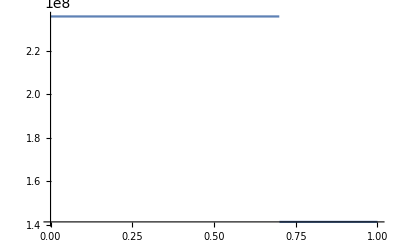

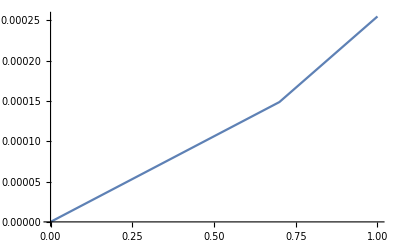

0.000148332

```mathematica
Plot[EA[X],{X,0,1}]
Plot[u[X],{X,0,1}]
```